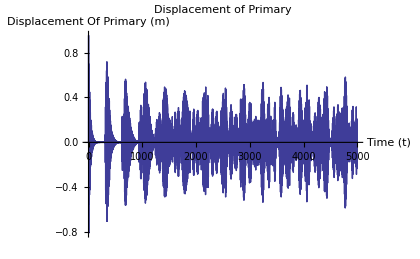

/Users/Gediz/Desktop/1.jpg

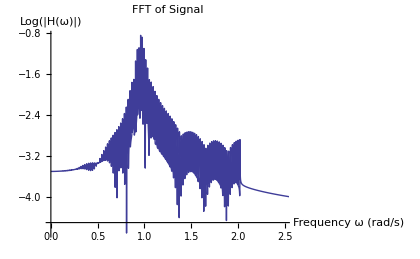

/Users/Gediz/Desktop/2.jpg

-Graphics3D-

/Users/Gediz/Desktop/3.jpg

-Graphics3D-

/Users/Gediz/Desktop/4.jpg

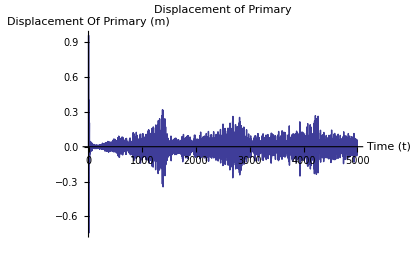

/Users/Gediz/Desktop/5.jpg

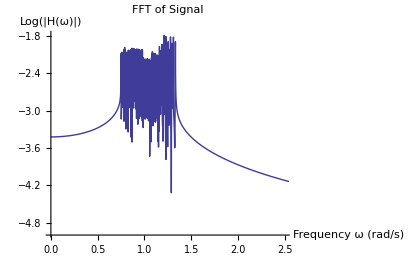

/Users/Gediz/Desktop/6.jpg

-Graphics3D-

/Users/Gediz/Desktop/7.jpg

-Graphics3D-

/Users/Gediz/Desktop/8.jpg

```mathematica
System[SetStdParams];
System[SymbolicPrecision]=12;
System[SetStdSysLin];
System[SetImpulseResp];
System[TIME]=5000;
System[FftMaxFreq]=2;
System[SolveSystem];
System[PrepareGraphs];

System[graph[3]]
Export[StringJoin["/Users/Gediz/Desktop/1.jpg"],%,ImageResolution->150]
System[graph[4]]
Export[StringJoin["/Users/Gediz/Desktop/2.jpg"],%,ImageResolution->150]
System[graph[5]]
Export[StringJoin["/Users/Gediz/Desktop/3.jpg"],%,ImageResolution->150]
System[graph[6]]
Export[StringJoin["/Users/Gediz/Desktop/4.jpg"],%,ImageResolution->150]


System[SetStdParams];
System[SymbolicPrecision]=12;
System[SetStdSysOpt];
System[SetImpulseResp];
System[TIME]=5000;
System[FftMaxFreq]=1.4;
System[SolveSystem];
System[PrepareGraphs];

System[graph[3]]
Export[StringJoin["/Users/Gediz/Desktop/5.jpg"],%,ImageResolution->150]
System[graph[4]]
Export[StringJoin["/Users/Gediz/Desktop/6.jpg"],%,ImageResolution->150]
System[graph[5]]
Export[StringJoin["/Users/Gediz/Desktop/7.jpg"],%,ImageResolution->150]
System[graph[6]]
Export[StringJoin["/Users/Gediz/Desktop/8.jpg"],%,ImageResolution->150]
```